# Lab_Work_2

# 1

```mathematica
1. Придумайте и определите символьное выражение t1, содержащее не менее трёх слагаемых, причём хотя бы одно из них должно быть рациональным выражением. Последовательно примените к нему функции Expand, ExpandAll, Factor, Together, Apart, Cancel, Simplify и объясните их действие. Выражение t1  должно быть таким, чтобы можно было проследить работу каждой из этих функций.
```

```mathematica
(*Out[2] Expand раскрывает скобки в выражении и представляет результат в виде суммы
Out[3] ExpandAll делает то же самое, но раскрывает скобки во всех частях выражения
Out[4] Factor раскладывает многочлен на множители
Out[5] Together приводит выражение к общему знаменателю
Out[6] Apart переписывает рациональное выражение как сумму членов с минимальными знаменателями
Out[7] Cancel сокращает на наибольший общий делитель числителя и знаменателя
Out[8] Simplify пытается расширить,разложить на множители и выполнить множество других преобразований в выражениях, чтобы получить простейшую возможную форму для результата.*)
```

```mathematica
t1 = 6(x^3-8)(x^2-y^2)/((2 x^2-8)(x-y)) +(x+y)^2+x^3+y^3
Expand[t1]
ExpandAll[t1]
Factor[t1]
Together[t1]
Apart[t1]
Cancel[t1]
Simplify[t1]
```

x^3+y^3+(x+y)^2+(6 (-8+x^3) (x^2-y^2))/((-8+2 x^2) (x-y))

x^2+x^3-(48 x^2)/((-8+2 x^2) (x-y))+(6 x^5)/((-8+2 x^2) (x-y))+2 x y+y^2+(48 y^2)/((-8+2 x^2) (x-y))-(6 x^3 y^2)/((-8+2 x^2) (x-y))+y^3

x^2+x^3+2 x y+y^2+y^3-(48 x^2)/(-8 x+2 x^3+8 y-2 x^2 y)+(6 x^5)/(-8 x+2 x^3+8 y-2 x^2 y)+(48 y^2)/(-8 x+2 x^3+8 y-2 x^2 y)-(6 x^3 y^2)/(-8 x+2 x^3+8 y-2 x^2 y)

((x+y) (12+8 x+6 x^2+x^3+2 y-x y-x^2 y+2 y^2+x y^2))/(2+x)

(12 x+8 x^2+6 x^3+x^4+12 y+10 x y+5 x^2 y+2 y^2+x y^2+2 y^3+x y^3)/(2+x)

(x (12+8 x+6 x^2+x^3))/(2+x)+((12+10 x+5 x^2) y)/(2+x)+y^2+y^3

x^3+y^3+(3 (4+2 x+x^2) (x+y))/(2+x)+(x+y)^2

(6 x^3+x^4+x^2 (8+5 y)+2 y (6+y+y^2)+x (12+10 y+y^2+y^3))/(2+x)

```mathematica
2. Приведите t1 к общему знаменателю и с помощью функции Numerator определите числитель полученного выражения (обозначьте t2). С помощью функции Collect представьте выражение t2 в виде полинома по степеням x или y. Определите максимальную степень n одной из переменных в t2 и коэффициент при (x^n).
```

```mathematica
(*Exponent [t2, x] выдаёт значение максимальной степени x в выражении t2
Coefficient[t2, n] выдает значение коэффициента перед выражением n в выражении t2*)
```

```mathematica
t1 = 6(x^3-8)(x^2-y^2)/((2 x^2-8)(x-y)) +(x+y)^2+x^3+y^3
t1 = Together[t1]
t2 = Numerator[t1]
t2 = Collect[t2, x]
n = Exponent[t2, x]
Coefficient[t2, x^n]
```

x^3+y^3+(x+y)^2+(6 (-8+x^3) (x^2-y^2))/((-8+2 x^2) (x-y))

(12 x+8 x^2+6 x^3+x^4+12 y+10 x y+5 x^2 y+2 y^2+x y^2+2 y^3+x y^3)/(2+x)

12 x+8 x^2+6 x^3+x^4+12 y+10 x y+5 x^2 y+2 y^2+x y^2+2 y^3+x y^3

6 x^3+x^4+12 y+2 y^2+2 y^3+x^2 (8+5 y)+x (12+10 y+y^2+y^3)

4

1

# 2

```mathematica
1. С помощью функции D вычислите производную функции x^n cos x.
```

```mathematica
(*D[f, x] даёт частную производную df/dx*)
```

```mathematica
D[x^n Cos[x],x]
```

n x^(-1+n) Cos[x]-x^n Sin[x]

```mathematica
2. Вычислите следующие производные
```

```mathematica
(*D[f, {x,n}] даёт частную производную d^n f/dx^n*)
```

```mathematica
D[(a x^3+2x^2), x]
D[(4x^2-5x+x-3/x), {x, 3}]
D[(x^3 y^2+3x^2), {x,3}, {y,2}]
```

4 x+3 a x^2

18/x^4

12

```mathematica
3. Вычислите интеграл
```

```mathematica
(*Integrate[f, x] даёт неопределённый интеграл fdx*)
```

```mathematica
Integrate[1/(x^2-1),x]
```

1/2 Log[1-x]-1/2 Log[1+x]

```mathematica
4. Вычислите интегралы и продифферентируйте результаты. При необходимости воспользуйтесь  функциями для преобразования выражений
```

```mathematica
f = (x^3 )/(x^2+1) 
f = Integrate[f, x]
expected = Simplify[D[f, x]]
```

x^3/(1+x^2)

x^2/2-1/2 Log[1+x^2]

x^3/(1+x^2)

```mathematica
f = 1/(x^3+1)
f = Integrate[f, x]
expected = Simplify[D[f, x]]
```

1/(1+x^3)

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

1/(1+x^3)

```mathematica
5. Вычислите определённый интеграл
```

```mathematica
(*Integrate[f, {x, xmin, xmax}] даёт определённый интеграл fdx в пределах от xmin до xmax*)
```

```mathematica
Integrate[(5x-2Sqrt[x]+32/(x^3)),{x,1,4}]
```

259/6

```mathematica
6. Вычислите интегралы (во втором случае не  целое число 1, а действительное число 1.)
```

```mathematica
f= (1+x^4)^(1/3)
Integrate[f ,{x,0,1}]
Integrate[f,{x,0,1.}]
```

(1+x^4)^(1/3)

Hypergeometric2F1[-1/3,1/4,5/4,-1]

1.05753

```mathematica
(*N[x] даёт числовое значение x
// выполняет объединение команд
Если в первом случае не добавить функцию N, то выведется гипергеометрическая функция "Hypergeometric2F1[-1/3,1/4,5/4,-1]"*)
```

# 3

```mathematica
1. Используя функцию Solve решить уравнение
```

```mathematica
(*Solve[f, x] пытается решить систему f уравнений или неравенств для переменных x*)
```

```mathematica
Solve[a x^4+x^2+3==0,x]
```

{{x→-(√(-1/a-(√(1-12 a))/a))/(√2)},{x→(√(-1/a-(√(1-12 a))/a))/(√2)},{x→-(√(-1/a+(√(1-12 a))/a))/(√2)},{x→(√(-1/a+(√(1-12 a))/a))/(√2)}}

```mathematica
2. Найти точное решение системы уравнений
```

```mathematica
(*&& позволяет объединить два условия, между которыми располагается*)
```

```mathematica
Solve[x^2+y==1&&y^2-x^2==2, {x,y}]
```

{{x→-ⅈ √(1/2 (-3+√13)),y→1/2 (-1+√13)},{x→ⅈ √(1/2 (-3+√13)),y→1/2 (-1+√13)},{x→-√(1/2 (3+√13)),y→1/2 (-1-√13)},{x→√(1/2 (3+√13)),y→1/2 (-1-√13)}}

```mathematica
3. Решить систему уравнений (если точечное решение найти не удаётся, получите численное решение)
```

```mathematica
(*NSolve[f, x] пытается найти численные приближения к решениям системы f уравнений или неравенств для переменных x*)
```

```mathematica
NSolve[x^2-y^2==1&&y^3+x==5, {x,y}]
```

{{x→-0.928941-1.39823 ⅈ,y→-0.788459-1.64735 ⅈ},{x→-0.928941+1.39823 ⅈ,y→-0.788459+1.64735 ⅈ},{x→1.78303,y→1.47621},{x→-2.17236,y→1.9285},{x→1.1236-1.05808 ⅈ,y→-0.913899+1.30087 ⅈ},{x→1.1236+1.05808 ⅈ,y→-0.913899-1.30087 ⅈ}}

```mathematica
4. Найдите решения дифференциальных уравнений. Задайте граничные условия и найлите соответствующие им частные решения. Постройте их графики
```

```mathematica
(*f /. rules или ReplaceAll[f, rules] применяет правило или список правил в попытке преобразовать каждую часть выражения f
Plot [f, {x, xmin, xmax}] генерирует график f как функцию от x (от xmin до xmax)*)
```

-Tan[x] y[x]+y'[x]==x

{{y[x]→C[1] Sec[x]+Sec[x] (Cos[x]+x Sin[x])}}

{{y[x]→6 Sec[x]+Sec[x] (Cos[x]+x Sin[x])}}

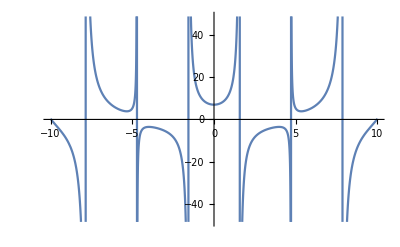

```mathematica
f = y'[x]-y[x]Tan[x]==x
result =DSolve[f,y[x],x]
result=result /.C[1] -> 6
Plot[y[x]/.result,{x,-10,10}]
```

```mathematica
5. Найдите решение дифференциального уравнения в символьном виде. Затем с помощью NDSolve найдите численное решения. Граничные условия и x выбрать самостоятельно. Построить графики обоих решений и показать,что они совпадают.
```

```mathematica
(*NDSolve[enqs, u, {x,xmin,xmax}] находит численное решение обыкновенных дифференциальных уравнений enqs для функции u с независимой переменной х в диапазоне хmin до хmax*)
```

Tan[x] y[x]+y'[x]==Sec[x]

{{y[x]→C[1] Cos[x]+Sin[x]}}

{{y[x]→Cos[x]+Sin[x]}}

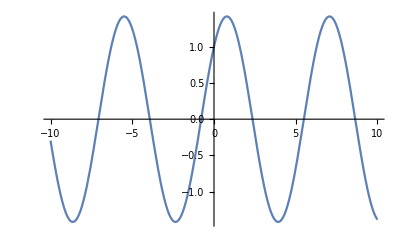

```mathematica
f = y'[x]+y[x]Tan[x]==1/Cos[x]
result =DSolve[f,y[x],x]
result=result /.C[1] -> 1
Plot[y[x]/.result,{x,-10,10}]
```

{x y[x]-y'[x]+y''[x]==0,y[0]==0,y'[0]==1}

{{y[x]→ⅇ^(x/2) π (AiryAi[1/4-x] AiryBi[1/4]-AiryAi[1/4] AiryBi[1/4-x])}}

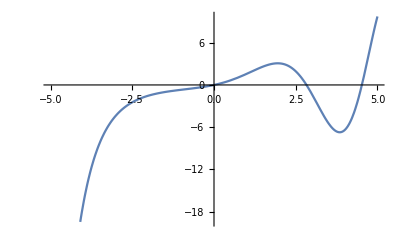

{{y[x]→InterpolatingFunction[…][x]}}

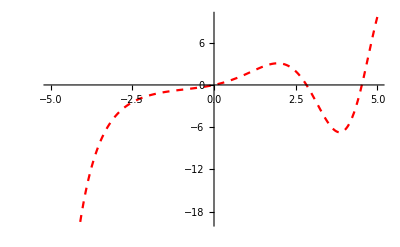

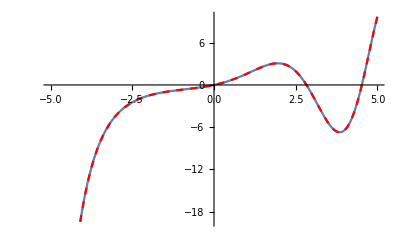

```mathematica
f = {y''[x]-y'[x]+x y[x]==0, y[0]==0, y'[0]==1}

sol1= DSolve[f,y[x],x]//FullSimplify
plt1 = Plot[sol1[[1,1,2]], {x,-5,5}]

sol2 = NDSolve[f, y[x],{x, -10, 10}]
plt2 = Plot[sol2[[1,1,2]],{x,-5,5}, PlotStyle->{Dashed, Red}]
Show[plt1, plt2]
(*Show[g1, g2,...] показывает несколько графиков вместе взятых*)
```

# 4

```mathematica
Выполните пункты 1,2,3 из примера по нахождению центра масс в методичке.
```

√2 √x

-√2 √x

2-3 x

√2 √x==y

-√2 √x==y

2-3 x==y

{{x→1/9 (7-√13),y→1/3 (-1+√13)}}

1/9 (7-√13)

{{x→1/9 (7+√13),y→1/3 (-1-√13)}}

1/9 (7+√13)

{{x→0,y→0}}

0

2-3 x==0

{{x→2/3,y→0}}

2/3

2/27 (-9+4 √3)+1/81 (73+13 √13)

(634+432 √3+286 √13)/(855+1080 √3+585 √13)

-(19+13 √13)/(57+72 √3+39 √13)

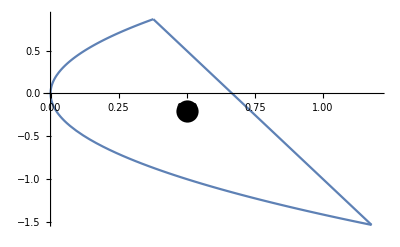

(4 (-45+8 √3) m)/(95+120 √3+65 √13)+(2 (127+13 √13) m)/(95+120 √3+65 √13)

(4 (-7+8 √3) m)/(7 (19+24 √3+13 √13))+(2 (1415+377 √13) m)/(189 (19+24 √3+13 √13))

(8 (-175+48 √3) m)/(35 (19+24 √3+13 √13))+(4 (15539+2171 √13) m)/(945 (19+24 √3+13 √13))

(4 (6089+2592 √3+2171 √13) m)/(945 (19+24 √3+13 √13))

0

```mathematica
exp1 = Sqrt[2x]
exp2 = -Sqrt[2x]
exp3 = -3x+2

f1 = exp1==y
f2 = exp2==y
f3 = exp3 ==y

(*Находим точки пересечения уравнений между собой Out[156-161]*)
sol1 =Solve[{f1, f3}, {x, y}]
x1 = x /. sol1[[1]]

sol2 = Solve[{f2, f3}, {x, y}]
x2 = x /. sol2[[1]]

sol3 = Solve[{f1, f2}, {x, y}]
x3 = x /. sol3[[1]]

f0 = exp3 ==0
sol0 = Solve[{f3, f0}, {x, y}]
x0 = x /. sol0[[1]]

(*Integrate[f, {x,xmin,xmax}, {y,ymin,ymax] даёт кратный интеграл $fdx$fdy
Найдём площадь заданной фигуры Out[162] и подставим его в выражения для нахождения центра масс Out[163-164]*)
s = Integrate[1, {x, x0, x3}, {y, exp1, exp3}] + Integrate[1, {x, x3, x2}, {y, exp2,  exp3}]
xc = Simplify[(1/m)(Integrate[(m/s)x, {x, x0, x3}, {y, exp1, exp3}] + Integrate[(m/s)x, {x, x3, x2}, {y, exp2,  exp3}])]
yc = Simplify[(1/m)(Integrate[(m/s)y, {x, x0, x3}, {y, exp1, exp3}] + Integrate[(m/s)y, {x, x3, x2}, {y, exp2,  exp3}])]

(*Построим заданную фигуру и найденный центр масс на графике*)

p1 = Plot[exp1, {x, x3, x1}, DisplayFunction-> Identity];
p2= Plot[exp2, {x, x3, x2}, DisplayFunction-> Identity];
p3= Plot[exp3, {x, x1, x2},DisplayFunction-> Identity];

Show[p1, p2, p3, Epilog -> {PointSize[0.04], Point[{xc, yc}]}, PlotRange->{{0,1.2},{-1.5,0.9}}, DisplayFunction-> $DisplayFunction]
(*До того как я узнал про PlotRange я использовал "Plot[2x-1.5, {x,0, 1.2},PlotStyle→{Dashed, Transparent}]," в самом начале скобки. Значения для PlotRange были высчитаны из этого невидимого графика, чтобы видеть всё изображение*)
(*Найдём моменты инерции и покажем, что ix + iy = iz*)
ix = Integrate[(m/s)y^2, {x, x0, x3}, {y, exp1, exp3}] + Integrate[(m/s)y^2, {x, x3, x2}, {y, exp2,  exp3}]
iy = Integrate[(m/s)x^2, {x, x0, x3}, {y, exp1, exp3}] + Integrate[(m/s)x^2, {x, x3, x2}, {y, exp2,  exp3}]
iz= Integrate[(m/s)(x^2+y^2), {x, x0, x3}, {y, exp1, exp3}] + Integrate[(m/s)(x^2+y^2), {x, x3, x2}, {y, exp2,  exp3}]

ii = Together[ix + iy]
Simplify[ii-iz]
```